```mathematica
F[n_,p_,a_,b_,f_]:=Sum[n!/(k!*(n-k)!) * p^k *(1-p)^(n-k)*Log[1+k*b*f -(n-k)*a*f],{k,0,n}]
G[n_,alpha_,beta_,a_,b_,f_]:=Sum[n!/(k!*(n-k)!)*Gamma[alpha+beta]*Gamma[k+alpha]*Gamma[n-k+beta]/(Gamma[alpha]*Gamma[beta]*Gamma[n+alpha+beta])*Log[1+k*b*f -(n-k)*a*f],{k,0,n}]
A[n_,p_,a_,b_]:= Maximize[{F[n,p,a,b,x],x≥0,x≤1/n},x]
B[n_,alpha_,beta_,a_,b_]:=Maximize[{G[n,alpha,beta,a,b,x],x≥0,x≤1/n},x]//N
```

```mathematica
Maximize[{F[100,0.6,1,1,x],x≥0,x≤1/100},x]
Maximize[{G[1,1.001,1.0,1,1,x],x≥0,x≤1/1},x]//N
Maximize[{F[10,1.001/2.001,1,1,x],x≥0,x≤1/10},x]
Maximize[{G[10,1.001,1.0,1,1,x],x≥0,x≤1/10},x]//N
```

{0.178947,{x→0.01}}

{1.24875×10^-7,{x→0.000499737}}

{1.24875×10^-6,{x→0.000499747}}

{3.12266×10^-7,{x→0.000124968}}

```mathematica
x/.A[20,0.6,1,1][[2]][[1]]
x/.B[20,3,2,1,1][[2]][[1]]
```

0.05

0.0416667

```mathematica
A[1,0.6,1,1][[1]]
A[5,0.6,1,1][[1]]
A[10,0.6,1,1][[1]]
```

0.0201355

0.0919273

0.14315

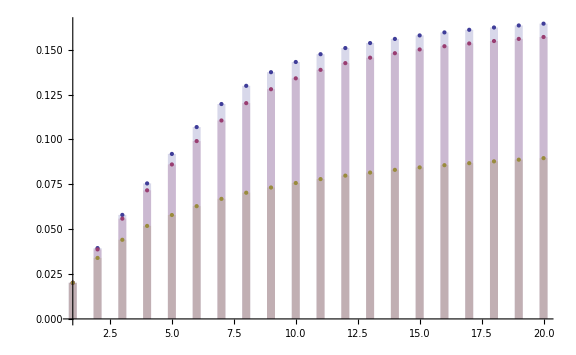

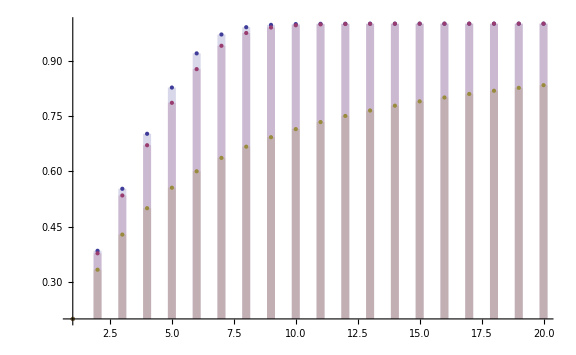

```mathematica
DiscretePlot[{A[n,0.6,1,1][[1]],B[n,30,20,1,1][[1]],B[n,3,2,1,1][[1]]},{n,1,20},ImageSize->Large,PlotStyle->{{Thickness[0.01],PointSize[Large]}}]
DiscretePlot[{(x/.A[n,0.6,1,1][[2]][[1]])*n,(x/.B[n,30,20,1,1][[2]][[1]])*n,(x/.B[n,3,2,1,1][[2]][[1]])*n},{n,1,20},ImageSize->Large,PlotStyle->{{Thickness[0.01],PointSize[Large]}}]
```